{{2.,1.66},{1.4,0.91},{1.2,0.66},{1.,0.4},{0.8,0.155},{0.75,0.09},{0.7,0.037},{0.65,0.00686},{0.6,0.00437},{0.4,0.00151},{0.2,0.00052},{0.03,0.000056},{0.,0}}

FittedModel[Piecewise[{{-0.000655758+0.00917582 x, x<0.680115}, {-0.847073+1.2537 x, x≥0.680115}, {0, True}}]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00917582 | 0.00565678 | 1.62209 | 0.139233
b | 1.2537 | 0.00312843 | 400.742 | 1.90978×10^-20
c | -0.000655758 | 0.00229012 | -0.286342 | 0.781098
k | 0.680115 | 0.00255573 | 266.113 | 7.60403×10^-19

{Piecewise[{{-0.847073+1.2537 x-2.26216 √(0.0000141109-0.000021951 x+9.78709×10^-6 x^2), x≥0.680115}, {-0.000655758+0.00917582 x-2.26216 √(5.24467×10^-6-0.0000200528 x+0.0000319992 x^2), True}}],Piecewise[{{-0.847073+1.2537 x+2.26216 √(0.0000141109-0.000021951 x+9.78709×10^-6 x^2), x≥0.680115}, {-0.000655758+0.00917582 x+2.26216 √(5.24467×10^-6-0.0000200528 x+0.0000319992 x^2), True}}]}

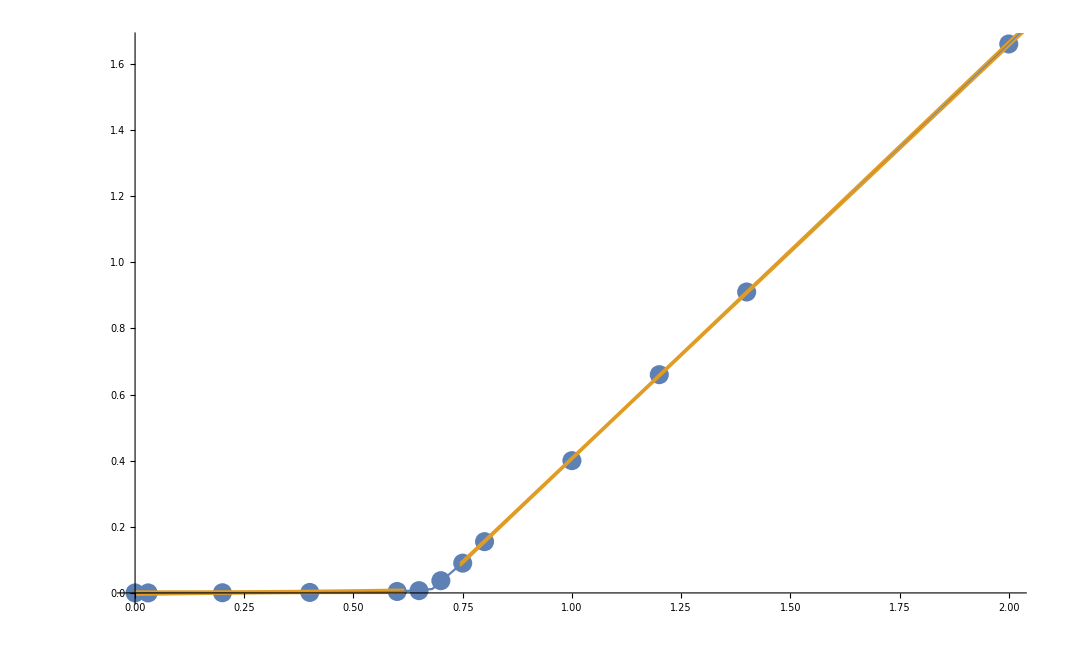

```mathematica
data = Import["~/phys3117/lab2/4.1", "tsv"][[12;;All,{1,2}]]
fit = NonlinearModelFit[data, Piecewise[{{a x + c, x < k}, {b x + (a k + c - b k), x ≥ k}}], {a, b, c, {k, 0.8}}, x]
fit["ParameterTable"]
fit["MeanPredictionBands"]
Show[ListPlot[data], Plot[{Normal[fit], fit["MeanPredictionBands"]}, {x, 0, 200}]]
```

```mathematica
Sqrt@Length[data] 1.96fit["ParameterErrors"]
```

{0.0399758,0.0221083,0.016184,0.0180611}